## Calculating the components of the total A.M. within polar coordinates

```mathematica
j[I_]:=Sqrt[I(I+1)];
I1[I_,theta_,phi_]:=j[I]*Sin[theta]*Cos[phi];
I2[I_,theta_,phi_]:=j[I]*Sin[theta]*Sin[phi];
I3[I_,theta_,phi_]:=j[I]*Cos[theta];
theta[I3_,I_]:=ArcCos[I3/j[I]];
phi[I2_,I1_]:=ArcTan[I2/I1];
```

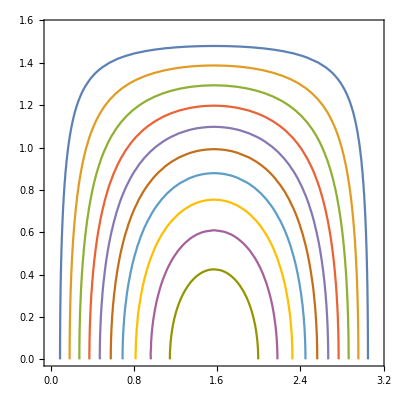

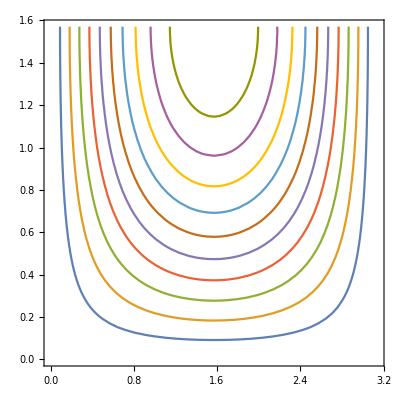

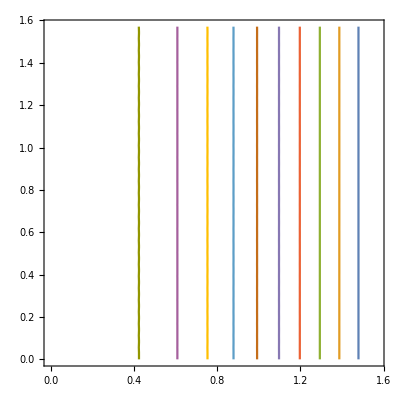

```mathematica
ContourPlot[{I1[j[10],x,y]==1,I1[j[10],x,y]==2,I1[j[10],x,y]==3,I1[j[10],x,y]==4,I1[j[10],x,y]==5,I1[j[10],x,y]==6,I1[j[10],x,y]==7,I1[j[10],x,y]==8,I1[j[10],x,y]==9,I1[j[10],x,y]==10},{x,0,π},{y,0,π/2}]
ContourPlot[{I2[j[10],x,y]==1,I2[j[10],x,y]==2,I2[j[10],x,y]==3,I2[j[10],x,y]==4,I2[j[10],x,y]==5,I2[j[10],x,y]==6,I2[j[10],x,y]==7,I2[j[10],x,y]==8,I2[j[10],x,y]==9,I2[j[10],x,y]==10},{x,0,π},{y,0,π/2}]
ContourPlot[{I3[j[10],x,y]==1,I3[j[10],x,y]==2,I3[j[10],x,y]==3,I3[j[10],x,y]==4,I3[j[10],x,y]==5,I3[j[10],x,y]==6,I3[j[10],x,y]==7,I3[j[10],x,y]==8,I3[j[10],x,y]==9,I3[j[10],x,y]==10},{x,0,π/2},{y,0,π/2}]
```

```mathematica
fig1=ContourPlot[{I1[j[10],x,y]},{x,0,π},{y,0,2π},AspectRatio->Automatic,Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ [rad]","φ [rad]"},ColorFunction->"BlueGreenYellow",Contours->Automatic,LabelStyle->{18,Bold,Black},PlotRange->All,ImageSize->280,PlotLabel->"I_1(θ,φ) ; I=10 ℏ",PlotLegends->Automatic];
fig2=ContourPlot[{I2[j[10],x,y]},{x,0,π},{y,0,2π},AspectRatio->Automatic,Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ [rad]","φ [rad]"},ColorFunction->"BlueGreenYellow",Contours->Automatic,LabelStyle->{18,Bold,Black},PlotRange->All,ImageSize->280,PlotLabel->"I_2(θ,φ) ; I=10 ℏ",PlotLegends->Automatic];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/angular-components-TRM/angular_components-TRM-1.pdf",fig1];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/angular-components-TRM/angular_components-TRM-2.pdf",fig2];
fig1
fig2
```

-Graphics-

-Graphics-

```mathematica
(*ContourLabels->(Style[Text[#3,{#1,#2}],Bold,12,Black,Background->LightBlue]&)*)
```

```mathematica
ContourPlot[{I2[j[10],x,y]},{x,0,π},{y,0,2π},AspectRatio->Automatic]
```